## Amitosis

## Model

We model the change in the distribution of the number i of mutations at a single locus in a population of diploids as a result of selection, mutation and reproduction by amitosis.

### Parameters

#### Genotype frequencies

x0, x1, and x2 represent the frequencies of the genotypes with 0, 1, and 2 mutations, respectively.

```mathematica
x={x0,x1,x2}
```

{x0,x1,x2}

#### Fitness

s < 0 is the deleterious effect of a mutation in a homozygous state.

```mathematica
w={1,1+s/2,1+s}
```

{1,1+s/2,1+s}

#### Mean fitness

Equation S2 (Supplementary Information)

```mathematica
w̄=Total[x w]
```

x0+(1+s/2) x1+(1+s) x2

### Evolution

#### Effect of selection

```mathematica
Δsel=(x w)/(w̄)-x
```

{-x0+x0/(x0+(1+s/2) x1+(1+s) x2),-x1+((1+s/2) x1)/(x0+(1+s/2) x1+(1+s) x2),-x2+((1+s) x2)/(x0+(1+s/2) x1+(1+s) x2)}

#### Effect of mutation

μ is the deleterious mutation rate.  We assume that (i) an individual can, at most, acquire one mutation, and (ii) mutations are irreversible.

```mathematica
Δmut={-2 μ x0,2 μ x0- μ x1,μ x1}
```

{-2 x0 μ,2 x0 μ-x1 μ,x1 μ}

#### Effect of reproduction

```mathematica
Δamit={x1/6,-x1/3,x1/6}
```

{x1/6,-x1/3,x1/6}

#### Combined effects of mutation, selection, and reproduction

Equation S9: genotype frequencies in the following generation

```mathematica
nextx=x+Δsel+Δmut+Δamit//Simplify
```

{x1/6+x0 (1/(x0+x1+(s x1)/2+x2+s x2)-2 μ),-x1/3+((2+s) x1)/(2 x0+(2+s) x1+2 (1+s) x2)+2 x0 μ-x1 μ,x1/6+((1+s) x2)/(x0+x1+(s x1)/2+x2+s x2)+x1 μ}

```mathematica
Simplify[nextx=={ x0/(w̄)-2 μ x0+x1/6,((2+s) x1)/(2 w̄)+2 μ x0- μ x1-x1/3,((1+s) x2)/(w̄)+μ x1+x1/6}]
```

True

## Equilibrium

### Equilibrium

There are three equilibria, but only the second and third equilibria have x0 > 0

```mathematica
sol=Solve[nextx==x,{x0,x1,x2}]//FullSimplify
```

{{x0→0,x1→0,x2→1},{x0→1/(16 s^2 (1+μ) (2+3 μ)^2)(2 (1+μ) (1+6 μ) (2+6 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))+s^2 (37+2 μ (71+18 μ (5+2 μ)))+s (12+9 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+4 μ (38+5 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+3 μ (24+12 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))))),x1→-1/(8 s^2 (1+μ) (2+3 μ)^2)(4+4 s-15 s^2+40 μ+52 s μ-72 s^2 μ+108 μ^2+60 s μ^2-120 s^2 μ^2+72 μ^3-72 s^2 μ^3+(2+5 s+14 (1+s) μ+12 (1+s) μ^2) √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)),x2→1/(16 s^2 (1+μ) (2+3 μ)^2)(1+6 μ) (-3 (s+2 s μ)^2+2 (1+μ) (2+6 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))+s (-4+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+2 μ (-12-12 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))))},{x0→1/(16 s^2 (1+μ) (2+3 μ)^2)(-2 (1+μ) (1+6 μ) (-2-6 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))+s^2 (37+2 μ (71+18 μ (5+2 μ)))+s (12-9 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+4 μ (38-5 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+3 μ (24+12 μ-√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))))),x1→1/(8 s^2 (1+μ) (2+3 μ)^2)(-4-4 s+15 s^2-40 μ-52 s μ+72 s^2 μ-108 μ^2-60 s μ^2+120 s^2 μ^2-72 μ^3+72 s^2 μ^3+(2+5 s+14 (1+s) μ+12 (1+s) μ^2) √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)),x2→-(((1+6 μ) (3 (s+2 s μ)^2+2 (1+μ) (-2-6 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))+s (4+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+2 μ (12+12 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)))))/(16 s^2 (1+μ) (2+3 μ)^2))}}

The second equilibrium does not produces valid genotype frequencies when x0 > 0

```mathematica
Reduce[{0<Values[sol[[2]][[1]]]≤1,0≤Values[sol[[2]][[2]]]≤1,0≤Values[sol[[2]][[3]]]≤1,0<μ<1,-1≤s<0}]
```

False

Equation S10

```mathematica
eq=sol[[3]]//FullSimplify
```

{x0→1/(16 s^2 (1+μ) (2+3 μ)^2)(-2 (1+μ) (1+6 μ) (-2-6 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))+s^2 (37+2 μ (71+18 μ (5+2 μ)))+s (12-9 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+4 μ (38-5 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+3 μ (24+12 μ-√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))))),x1→1/(8 s^2 (1+μ) (2+3 μ)^2)(-4-4 s+15 s^2-40 μ-52 s μ+72 s^2 μ-108 μ^2-60 s μ^2+120 s^2 μ^2-72 μ^3+72 s^2 μ^3+(2+5 s+14 (1+s) μ+12 (1+s) μ^2) √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)),x2→-1/(16 s^2 (1+μ) (2+3 μ)^2)(1+6 μ) (3 (s+2 s μ)^2+2 (1+μ) (-2-6 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))+s (4+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+2 μ (12+12 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))))}

```mathematica
α=√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2);β=1/(16 s^2 (1+μ) (2+3 μ)^2);
```

```mathematica
Simplify[eq=={x0->β(4+s (12+37 s)+40 μ+2 s (76+71 s) μ+36 (1+s) (3+5 s) μ^2+72 (1+s)^2 μ^3-α (2 (1+μ) (1+6 μ)+s (9+4 μ (5+3 μ)))),x1->2β(3 s^2 (1+2 μ) (5+2 μ (7+6 μ))+2(1+μ) (1+6 μ) (-2+α-6 μ) +s (-4+5 α+2 μ (-26+7 α+6 (-5+α) μ))),x2->-β(1+6 μ) (3 (s+2 s μ)^2+2 (1+μ) (-2+α-6 μ)+s (4+α+2 μ (12+α+12 μ)))}]
```

True

### Stability

#### Jacobian matrix

```mathematica
f=nextx/.{x2->1-x0-x1}//FullSimplify
```

{x1/6-(2 x0)/(-2+s (-2+2 x0+x1))-2 x0 μ,-x1/3-((2+s) x1)/(-2+s (-2+2 x0+x1))+2 x0 μ-x1 μ,x1/6+(2 (1+s) (-1+x0+x1))/(-2+s (-2+2 x0+x1))+x1 μ}

Equation S11

```mathematica
j=({{D[f[[1]],x0], D[f[[1]],x1]}, {D[f[[2]],x0], D[f[[2]],x1]}})//Simplify
```

{{(4 s x0)/(-2+s (-2+2 x0+x1))^2-2/(-2+s (-2+2 x0+x1))-2 μ,1/6+(2 s x0)/(-2+s (-2+2 x0+x1))^2},{2 ((s (2+s) x1)/(-2+s (-2+2 x0+x1))^2+μ),-1/3+(s (2+s) x1)/(-2+s (-2+2 x0+x1))^2-(2+s)/(-2+s (-2+2 x0+x1))-μ}}

```mathematica
Simplify[j=={{1/(w̄)+(s x0)/(w̄)^2-2 μ,1/6+(s x0)/(2(w̄)^2)},{(s (2+s) x1)/(2(w̄)^2)+2μ,-1/3+(2+s)/(2 w̄)+(s (2+s) x1)/(4(w̄)^2)-μ}}/.{x2->1-x0-x1}]
```

True

#### Jacobian matrix evaluated at equilibrium

```mathematica
jeq=j/.eq//FullSimplify
```

{{1/(18 s (2+s))(9 s^3 (1+2 μ)^2-2 (1+6 μ) (-2-6 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))+s (52-11 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+6 μ (17+30 μ-3 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)))-3 s^2 (-9+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+2 μ (-17-24 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)))),1/(36 s (2+s))(9 s^3 (1+2 μ)^2-3 s^2 (1+2 μ) (-8-24 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))-2 (1+6 μ) (-2-6 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))+2 s (11-4 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+3 μ (20+30 μ-3 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))))},{1/(9 s (2+s))(-9 s^3 μ (1+2 μ)+2 (1+6 μ) (-2-6 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))+s (-4+5 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)-3 μ (8+42 μ-5 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)))+3 s^2 (5+μ (1-24 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)))),1/(36 s (2+s))(s^3 (9-36 μ^2)+4 (1+6 μ) (-2-6 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))+3 s^2 (26-√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+2 μ (4-24 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)))+s (4 (13+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))+6 μ (-14-42 μ+5 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))))}}

#### Characteristic equation of the Jacobian matrix

Equation S12

```mathematica
a=CoefficientList[CharacteristicPolynomial[jeq,y],y]//FullSimplify
```

{1/(108 (2+s)^2)(27 s^4 (1+2 μ)^3+9 s^3 (1+2 μ) (19-√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+2 μ (35+36 μ-√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)))-4 s (-197+46 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)-3 μ (186-32 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+3 μ (97+60 μ-9 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))))+4 (134-31 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+3 μ (82-16 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+3 μ (38+18 μ-5 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))))+3 s^2 (122-21 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+2 μ (313-32 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+6 μ (103+72 μ-5 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))))),1/12 (-26+3 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)-3 s (3+4 μ (2+μ))+1/(2+s)2 μ (-20-18 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+s (-14-12 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)))),1}

```mathematica
Simplify[a=={1/(108 (2+s)^2)(4 (134-31 α+3 μ (82-16 α+3 μ (38-5 α+18 μ)))+4 s (197-46 α+3 μ (186-32 α+3 μ (97-9 α+60 μ)))+3 s^2 (122-21 α+2 μ (313-32 α+6 μ (103-5 α+72 μ)))+9 s^3 (1+2 μ) (19-α+2 μ (35-α+36 μ))+27 s^4 (1+2 μ)^3),-1/12 (26-3 α+3 s (3+4 μ (2+μ))+(2 μ)/(2+s)(20-α+18 μ+s (14-α+12 μ))),1}]
```

True

```mathematica
pol[λ_]:=a[[1]]+a[[2]]λ+λ^2
```

```mathematica
b=CoefficientList[pol[y+1],y]//FullSimplify
```

{1/(108 (2+s)^2)(27 s^4 (1+2 μ)^3-4 (-2 (1+3 μ)^2 (4+9 μ)+4 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+39 μ √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+45 μ^2 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))+6 s^2 (2+3 μ) (-7-3 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+2 μ (37+72 μ-5 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)))+9 s^3 (1+2 μ) (10-√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+2 μ (32+36 μ-√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)))+s (-40-76 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+6 μ (84-55 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+6 μ (64+60 μ-9 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))))),1/12 (-2+3 √((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)-3 s (3+4 μ (2+μ))+1/(2+s)2 μ (-20-18 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)+s (-14-12 μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2)))),1}

```mathematica
Simplify[b=={1+a[[1]]+a[[2]],2+a[[2]],1}]
```

True

#### Stability condition

Equations S13 and S14: Routh-Hurwitz conditions for stability

```mathematica
stab=Reduce[{b[[1]]>0,b[[2]]>0,0<μ<1,-1≤s<0}]
```

(-1≤s≤1/31 (-21+√7)&&0<μ<1)||(1/31 (-21+√7)<s<0&&0<μ<1/12 √((1-11 s)/(1+s))+(-1-7 s)/(12 (1+s)))

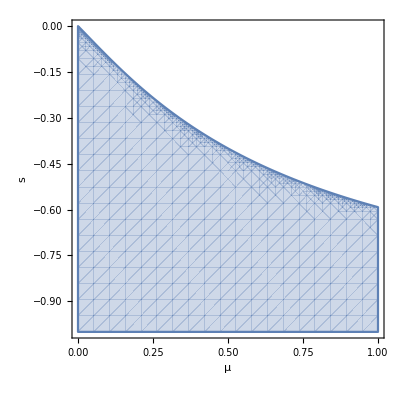

```mathematica
RegionPlot[stab,{μ,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

The equilibrium is also valid if the stability condition is met.

```mathematica
valid=Reduce[{0≤Values[eq[[1]]]≤1,0≤Values[eq[[2]]]≤1,0≤Values[eq[[3]]]≤1,0<μ<1,-1≤s<0}]
```

(-1≤s≤1/31 (-21+√7)&&0<μ<1)||(1/31 (-21+√7)<s<0&&0<μ≤1/12 √((1-11 s)/(1+s))+(-1-7 s)/(12 (1+s)))

### Mean fitness at equilibrium (1 locus)

Equation S15

```mathematica
ŵ=w̄/.eq//FullSimplify
```

(14+3 s+6 (3+s) μ+√((2-3 s)^2+12 (2+3 s (1+s)) μ+36 (1+s)^2 μ^2))/(8 (1+μ) (2+3 μ))

```mathematica
Simplify[ŵ==(14+3 s+6 (3+s) μ+α)/(8 (1+μ) (2+3 μ))]
```

True

### Mean fitness at equilibrium (L loci)

If there are L fitness loci with the same μ and s, and there is linkage equilibrium between the loci, the mean fitness at equilibrium will be (ŵ)^L.  Taking a first-order Taylor expansion of ln((ŵ)^L) we get

```mathematica
FullSimplify[Series[Log[(ŵ)^L],{μ,0,1}],Assumptions->2-3 s>0]
```

(L (2-6 s) μ)/(-2+3 s)+O[μ]^2

Equation S16 and Equation 2 (main text)

```mathematica
Solve[Log[y]==(L (2-6 s) μ)/(-2+3 s),{y}]
```

{{y→ConditionalExpression[ⅇ^(-(2 L (-1+3 s) μ)/(-2+3 s)),-π<-2 Im[(L (-1+3 s) μ)/(-2+3 s)]≤π]}}

U is the deleterious mutation rate per diploid genome per generation.

```mathematica
U=2L μ
```

2 L μ

```mathematica
Simplify[ⅇ^(-(2 L (-1+3 s) μ)/(-2+3 s))==ⅇ^(-U((1-3 s)/(2-3 s)))]
```

True

## Numerical calculations

```mathematica
Clear[U]
```

```mathematica
ⅇ^-U/.{U->0.1}
```

0.904837

```mathematica
ⅇ^(-U((1-3 s)/(2-3 s)))/.{U->0.1,s->-0.1}
```

0.945046

```mathematica
ⅇ^(-U((1-3 s)/(2-3 s)))/ⅇ^-U-1/.{U->0.1,s->-0.1}
```

0.0444373

```mathematica
ⅇ^(-U((1-3 s)/(2-3 s)))/ⅇ^-U-1/.{U->0.2,s->-0.1}
```

0.0908493

```mathematica
ⅇ^(-U((1-3 s)/(2-3 s)))/ⅇ^-U-1/.{U->0.1,s->-0.01}
```

0.0504946